# Speed Comparison.

Below is the code that is needed to be run in order to compute cells further down the page.

### Code:

```mathematica
LT[p_?PolynomialQ,vars_,or_]:=First[MonomialList[p,vars,or]]
```

```mathematica
lc[f_,g_,vars_List,or_]:=With[{w=PolynomialLCM[LT[f,vars,or],LT[g,vars,or]]},w/(w/.Thread[vars->1])]
```

```mathematica
S[f_,g_,vars_List,or_]:=(f lc[LT[f,vars,or],LT[g,vars,or],vars,or])/LT[f,vars,or]-(g lc[LT[f,vars,or],LT[g,vars,or],vars,or])/LT[g,vars,or]
```

```mathematica
grobbasic[F_,order_]:= Module[{var,F1,F2, prem, a1,div},
var = Variables[F]; 
F1 = F;
div ={x};
     prem = Subsets[F1, {2} ];

While[ AllTrue[div, NumberQ ]!=True, 

a1 = Simplify[S[First[prem[[#]]], Last[prem[[#]]], var, order]] &/@ Range[Length[prem]];
div= PolynomialMod[#, F1] &/@ a1;
F1 = DeleteDuplicates[ DeleteCases[ Flatten[ Append[F1, div]], 0]];
];
Return[MonomialReduce[F1,order] ];
]
```

```mathematica
grobbasic2[F_,order_]:= Module[{var,q,r,F1, prem, a1,div},
var = Variables[F]; 
F1 = F;
r ={x};
     prem = Subsets[F1, {2} ];

While[ AllTrue[div, NumberQ ]!=True, 

a1 = Simplify[S[First[prem[[#]]], Last[prem[[#]]], var, order]] &/@ Range[Length[prem]];
{q,r}=PolynomialReduce[ # ,F1,var,MonomialOrder-> order]&/@ a1;
F1 = DeleteDuplicates[ DeleteCases[ Flatten[ Append[F1, r]], 0]];
];

Return[MonomialReduce[F1,Lexicographic] ];

]
```

```mathematica
LP[{i_,j_}]:=If[i<j, {i,j},{j,i}]
```

```mathematica
Crit[{i_, j_}, vars_, G_, B_] := Module[{q, r},
  For[l = 1, l <= Length[G], l++,
   If[MemberQ[B, LP[{i, l}]] || MemberQ[B, LP[{j, l}]] || MemberQ[{i, j}, l],
     Nothing,
     {q, r} = PolynomialReduce[lc[Part[G, i], Part[G, j], vars, Lexicographic], LT[Part[G, l], vars, Lexicographic], vars];
     If[r == 0, Return[True]; Break[];, Nothing];
     ];
   ];
  Return[False];
  ]
```

```mathematica
MonomialReduce[F_,ord_]:=Module[{i,j,q,r,k,B,G,K,R,pos,vars},
vars=Variables[F];
K=CoefReduce[F,Lexicographic];
G={};

For[i=1,i≤ Length[K],i++,
G=AppendTo[G,LT[Part[K,i],vars,Lexicographic]];
];
R={};
B=G;

For[j=1,j≤ Length[B],j++,
k=Part[B,j];
pos=Position[G,k];

{q,r}=PolynomialReduce[k,Delete[G,First[pos]],vars,MonomialOrder-> ord];
If[r==0,
G=Delete[G,First[pos]];
R=AppendTo[R,{j}],
Nothing];
];

G=Delete[K,R];
Return[G];
]
```

```mathematica
ImpGrob[F_,ord_]:=Module[{s,t,p,i,j,q,r,a,b,k,vars,G,B},
s=Length[F];
B={};
vars=Variables[F];

For[a=1,a≤ s-1,a++, Do[AppendTo[B,{a,b}],{b,a+1,s}]];
G=F;
t=s;

While[Length[B]≠ 0,
p=Part[B,1];
i=Part[p,1];
j=Part[p,2];

If[lc[Part[G,i],Part[G,j],vars,ord]=!=LT[Part[G,i],vars,ord]*LT[Part[G,j],vars,ord] && Crit[{i,j},vars,G,B]==False,
{q,r}=PolynomialReduce[S[Part[G,i],Part[G,j],vars,ord],G,vars,MonomialOrder-> ord];
If[r=!=0,
t=t+1;
AppendTo[G,r];
For[k=1,k≤ t-1,k++,AppendTo[B,{k,t}]]
,Nothing]
,Nothing];
B=Delete[B,1];
];
G=MonomialReduce[G,Lexicographic];
Return[G];
]
```

```mathematica
CoefReduce[F_,ord_]:=Module[{i,j,G,vars,temp},
vars=Variables[F];
G={};
For[i=1,i≤ Length[F],i++,
temp=LT[Part[F,i],vars,ord];
For[j=1,j≤ Length[vars],j++,temp=ReplaceAll[temp,Indexed[x,j]-> 1]];
G=AppendTo[G,Expand[Simplify[Part[F,i]/temp]]];
];
Return[G];
]
```

```mathematica
divalg[p_, q_,or_]:= Module[{vardiv,ltp, ltq, ltdiv,divindex,tf,rem,i,remq,test, hold , poly,varindex, testf,testpos,j},
rem = # &/@{p} ;
vardiv = Variables[Flatten[{p,q}]];
i=1;
hold = {};

While[  NumberQ[Last[rem]] ==False,
{      
	ltp = LT[rem[[i]],vardiv,or];

	ltq = LT[#,vardiv,or]& /@q ;

	ltdiv = ltp/# &/@ ltq;

tf =PolynomialQ[#,vardiv] & /@ ltdiv;

If[AnyTrue[tf, TrueQ], varindex=varindex,
j=1;
varindex =1;
While[ j  ≤ Length[vardiv] , {  

			ltp = LT[rem[[i]],vardiv[[varindex]],or];
			ltq = LT[#,vardiv,or]& /@q ;
			ltdiv = ltp/# &/@ ltq;
			tf =PolynomialQ[#,vardiv] & /@ ltdiv;

	If[AnyTrue[tf, TrueQ], Break[] ,varindex= varindex +1];
};
	j++;
];
If[AnyTrue[tf, TrueQ], , Break[]];

];


divindex = Flatten[Position[tf,True]];


remq = Simplify[ltdiv[[#]]* q[[#]]] &/@divindex ;


hold = Append[hold, (First[ ltdiv[[#]] &/@divindex ])*( First[ q[[#]] &/@divindex ])];

test = Simplify[rem[[i]] - remq[[#]] ]&/@Range[Length[divindex]]  ;

testf =PolynomialQ[#,vardiv] & /@ test;


testpos = FirstPosition[testf,True];

rem = Append[rem , First[test[[testpos]]] ];

poly = Last[rem]+  Plus @@ ( hold[[#]] &/@ Range[i] );   
};
 i++];

Last[rem]
]
```

## Graphs programs

Block of code to set g for later on.

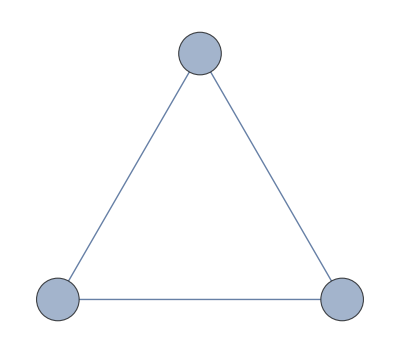

```mathematica
While@Not@ConnectedGraphQ[g=RandomGraph[{3,3},VertexLabels-> Placed[Automatic,Center],VertexSize->0.15]]
g
```

Block of code to generate a random graph based on the number of vertices needed.

```mathematica
graphgen[n_]:= Module[{g},
While@Not@ConnectedGraphQ[ g=RandomGraph[{n ,RandomInteger[{n-1, n(n-1)/2}] },VertexLabels-> Placed[Automatic,Center],VertexSize->0.15]];
Return[g]
]
```

Function to generate the polynomial system to be used in the GroebnerBasis.

```mathematica
kgraphploy[g_, k_]:= Module[{vert,absvert,edge,absedge, vertpoly, vars,edgepoly, graphpoly}, 
vert=VertexList[g];
absvert=Length[vert];


edge=List @@@EdgeList[g];
absedge=Length[edge];

vertpoly={};
For[i=1,i≤absvert,i++,AppendTo[vertpoly,Indexed[x,i]^k-1]];

vars=Variables[vertpoly];

edgepoly={};
For[i=1,i≤absedge,i++,AppendTo[edgepoly,Part[PolynomialReduce[Indexed[x,Part[Part[edge,i],1]]^k-Indexed[x,Part[Part[edge,i],2]]^k,Indexed[x,Part[Part[edge,i],1]]-Indexed[x,Part[Part[edge,i],2]],{Indexed[x,Part[Part[edge,i],1]],Indexed[x,Part[Part[edge,i],2]]}],1]]];
edgepoly=Flatten[edgepoly];

graphpoly=Join[vertpoly,edgepoly];

Return[graphpoly];
]
```

## Speed Comparison between the different methods of the built -in function.

Here we begin the Comparison of the different functions we used during the project. Namely the built in function and two of our own built functions based on the Buchberger Algorithm.

### Increasing the number of Colours Comparison.

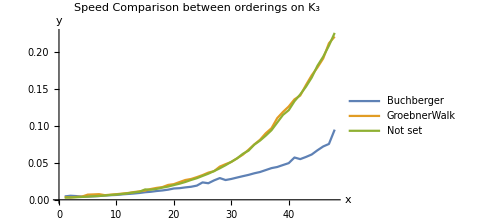
-Graphics-Number of colours (k)Times (Seconds)

```mathematica
upperlimitone = 50;
timebuiltinB = Table[First[ AbsoluteTiming[GroebnerBasis[kgraphploy[g,n], Variables[kgraphploy[g,n]],Method->"Buchberger"]]], {n,3,upperlimitone}];
timebuiltinW = Table[First[ AbsoluteTiming[GroebnerBasis[kgraphploy[g,n], Variables[kgraphploy[g,n]],Method->"GroebnerWalk"]]], {n,3,upperlimitone}];
timebuiltinU = Table[First[ AbsoluteTiming[GroebnerBasis[kgraphploy[g,n], Variables[kgraphploy[g,n]]]]], {n,3,upperlimitone}];

SCDMplot1 = Labeled[ListLinePlot[{timebuiltinB, timebuiltinW, timebuiltinU}, PlotLegends->{"Buchberger","GroebnerWalk","Not set"},PlotLabel->"Speed Comparison between orderings on K_3", AxesLabel->{"x","y"},ImageSize->Medium ],{"Number of colours (k)","Times (Seconds)"},{Bottom,Left},RotateLabel->True]
```

#### Increasing the number of vertices Comparison .

This program needs adjustment and or a long run time for decent set of data.

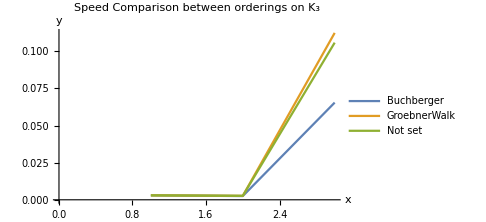
-Graphics-Number Vetrices (Starting at 3)Times (Seconds)

```mathematica
upperlimittwo = 9;
timebuiltinB2 = {};
timebuiltinW2 ={};
timebuiltinU2 = {};
i=3;
While[ i <= upperlimittwo, {   grun = kgraphploy[graphgen[i],5],

AppendTo[timebuiltinB2, First[ AbsoluteTiming[GroebnerBasis[grun,Variables[grun], Method->"Buchberger" ]] ]],
AppendTo[timebuiltinW2, First[AbsoluteTiming[GroebnerBasis[grun,Variables[grun], Method->"GroebnerWalk"]] ]],
AppendTo[timebuiltinU2, First[AbsoluteTiming[GroebnerBasis[grun,Variables[grun] ]] ] ] };
; i++ 
]

SCDMplot2 = Labeled[ListLinePlot[{timebuiltinB2, timebuiltinW2, timebuiltinU2}, PlotLegends->{"Buchberger","GroebnerWalk","Not set"},PlotLabel->"Speed Comparison between orderings on K_3", AxesLabel->{"x","y"},ImageSize->Medium ],{"Number Vetrices (Starting at 3)","Times (Seconds)"},{Bottom,Left},RotateLabel->True]
```

### Ordering

First we need to define the ordering. We do this as follows:

Lexicographic

```mathematica
A1=IdentityMatrix[3];
A1 // MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Degree Lexicographic

```mathematica
A2 = {{1,1,1},{1,0,0},{0,1,0}};
A2 // MatrixForm
```

(1 | 1 | 1
1 | 0 | 0
0 | 1 | 0)

Degree reverse Lexicographic

```mathematica
A3=  {{1,1,1},{0,0,-1},{0,-1,0}};
A3 // MatrixForm
```

(1 | 1 | 1
0 | 0 | -1
0 | -1 | 0)

### Increasing the number of vertices Comparison .

This program needs adjustment and or a long run time for decent set of data .

```mathematica
upperlimitone = 50;
timebuiltina1 = Table[First[ AbsoluteTiming[GroebnerBasis[kgraphploy[g,n], Variables[kgraphploy[g,n]],Method->"Buchberger",MonomialOrder->A1 ]]], {n,3,upperlimitone}];
timebuiltina2 = Table[First[ AbsoluteTiming[GroebnerBasis[kgraphploy[g,n], Variables[kgraphploy[g,n]],Method->"Buchberger",MonomialOrder->A2 ]]], {n,3,upperlimitone}];
timebuiltina3 = Table[First[ AbsoluteTiming[GroebnerBasis[kgraphploy[g,n], Variables[kgraphploy[g,n]],Method->"Buchberger",MonomialOrder->A3 ]]], {n,3,upperlimitone}];
```

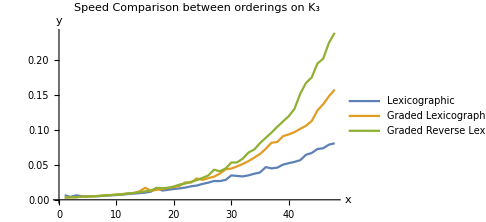
-Graphics-Number of colours (k)Times (Seconds)

```mathematica
SCDMplot3 =Labeled[ListLinePlot[{timebuiltina1, timebuiltina2, timebuiltina3}, PlotLegends->{"Lexicographic","Graded Lexicographic  ","Graded Reverse Lexicographic"},PlotLabel->"Speed Comparison between orderings on K_3", AxesLabel->{"x","y"},ImageSize->Medium ],{"Number of colours (k)","Times (Seconds)"},{Bottom,Left},RotateLabel->True]
```

```mathematica
Export["ordering_builtin_one.jpeg", SCDMplot3]
```

ordering_builtin_one.jpeg

## Speed Comparison between the different methods of the our coded functions .

The below block of code is to compare our basic and improved algorithm.

```mathematica
This program needs adjustment and or a long run time for decent set of data.
```

```mathematica
upperlimitone = 30;
timebasica1 = Table[First[ AbsoluteTiming[grobbasic[kgraphploy[g,n],A1 ]]], {n,3,upperlimitone}];
timebasica2 = Table[First[ AbsoluteTiming[grobbasic[kgraphploy[g,n],A2 ]]], {n,3,upperlimitone}];
timebasica3 = Table[First[ AbsoluteTiming[grobbasic[kgraphploy[g,n],A3 ]]], {n,3,upperlimitone}];

timeimpa1 = Table[First[ AbsoluteTiming[ImpGrob[kgraphploy[g,n],A1 ]]], {n,3,upperlimitone}];
timeimpa2 = Table[First[ AbsoluteTiming[ImpGrob[kgraphploy[g,n],A2 ]]], {n,3,upperlimitone}];
timeimpa3 = Table[First[ AbsoluteTiming[ImpGrob[kgraphploy[g,n],A3 ]]], {n,3,upperlimitone}];
```

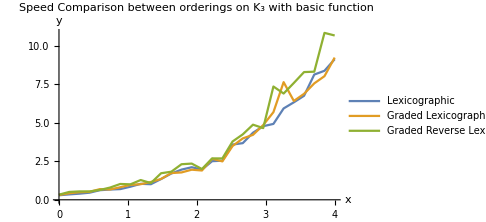
-Graphics-Number of colours (k)Times (Seconds)

```mathematica
SCOCplot1= Labeled[ListLinePlot[{timebasica1, timebasica2, timebasica3}, DataRange-> {0,4},PlotLegends->{"Lexicographic","Graded Lexicographic  ","Graded Reverse Lexicographic"},PlotLabel->"Speed Comparison between orderings on K_3 with basic function", AxesLabel->{"x","y"},ImageSize->Medium ],{"Number of colours (k)","Times (Seconds)"},{Bottom,Left},RotateLabel->True]
```

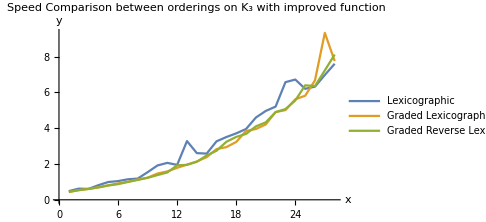
-Graphics-Number of colours (k)Times (Seconds)

```mathematica
SCOCplot2= Labeled[ListLinePlot[{timeimpa1, timeimpa2, timeimpa3}, PlotLegends->{"Lexicographic","Graded Lexicographic  ","Graded Reverse Lexicographic"},PlotLabel->"Speed Comparison between orderings on K_3 with improved function", AxesLabel->{"x","y"},ImageSize->Medium ],{"Number of colours (k)","Times (Seconds)"},{Bottom,Left},RotateLabel->True]
```

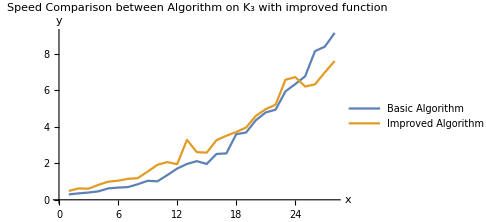
-Graphics-Number of colours (k)Times (Seconds)

```mathematica
SCOCplot3= Labeled[ListLinePlot[{timebasica1, timeimpa1}, PlotLegends->{"Basic Algorithm","Improved Algorithm "},PlotLabel->"Speed Comparison between Algorithm on K_3 with improved function", AxesLabel->{"x","y"},ImageSize->Medium ],{"Number of colours (k)","Times (Seconds)"},{Bottom,Left},RotateLabel->True]
```